```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/chenyr/工作区/ModelA_realsystem/crit_behav/exam/buffer

```mathematica
a=Flatten[Import["a.dat"]];
b=Flatten[Import["b.dat"]];
c=Flatten[Import["c.dat"]];
```

```mathematica
a//Length
```

31

```mathematica
ρmin=0;
ρmax=45000;
```

```mathematica
V1=Sum[a[[n+1]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,30}]+1/2 First[a];
```

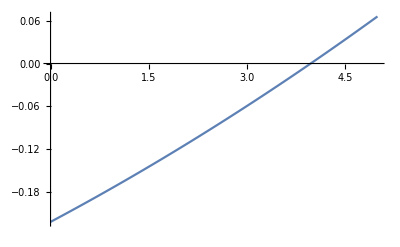

```mathematica
Plot[V1,{ρ,0,5}]
```

```mathematica
eqn=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,{10^-3,10^-2,10^-1,1,10,10^2,10^3,10^4,10^5,1.75*10^6}}];
```

```mathematica
res=Flatten[ParallelMap[FindRoot[#,{ρ,1000},WorkingPrecision->40]&,eqn]][[All,2]]
```

{3813.28290231031356881715614456556665338,3813.282908031484179639424941082383794678,3813.28296524318675716500799039036432638,3813.283537359859463342454021341143515617,3813.289258491280249371460901534126485452,3813.346466275492486830541265293215935933,3813.918191748594764247361426407512811903,3819.600826342577682423529891550112141998,3873.469919602188070765129279681386731918,4547.82077724466769554908897781441797057}

```mathematica
Sqrt[2*res]
```

{87.33021129380500438337960553200440616182,87.33021135931693346172146091476636821491,87.33021201443618111290977202514976047901,87.3302185656243444093658912780758399308,87.33028407707466342833843332329368693424,87.3309391484540544767443542545801060445,87.33748555744657759350430105758262991489,87.40252658067245692456621649749582805373,88.01670204685231298109260744446272601495,95.37107294399772763362913745047017774543}

```mathematica
mpi2=Sqrt[Sum[list2[[n]]*Cos[n*ArcCos[(2res-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]]
```

{0.0033839,0.0107008,0.033839,0.107008,0.33839,1.07008,3.38376,10.6964,33.7068,135.46}